# Create x-y Plot of Distances

```mathematica
SetDirectory[NotebookDirectory[]];
xyCoords=Import["TravelTim1_test.dat"]
```

{{12602,5915},{11746,11976},{13674,2963},{5028,11523},{4166,8309},{7160,9433},{5471,7701},{14283,13742},{9535,10759},{2124,9104},{244,3643}}

```mathematica
distmat=DistanceMatrix[xyCoords]//N
```

{{0.,6121.15,3140.62,9424.18,8769.11,6480.1,7351.26,8005.48,5733.31,10952.5,12565.1},{6121.15,0.,9216.91,6733.26,8420.41,5243.88,7592.84,3091.14,2523.81,10041.5,14203.3},{3140.62,9216.91,0.,12166.6,10907.9,9181.13,9473.01,10796.2,8826.6,13081.1,13447.2},{9424.18,6733.26,12166.6,0.,3327.59,2985.55,3847.59,9517.3,4571.3,3779.52,9218.52},{8769.11,8420.41,10907.9,3327.59,0.,3198.03,1439.68,11483.5,5901.58,2191.3,6095.38},{6480.1,5243.88,9181.13,2985.55,3198.03,0.,2419.2,8324.94,2720.09,5046.74,9019.71},{7351.26,7592.84,9473.01,3847.59,1439.68,2419.2,0.,10683.9,5086.01,3629.16,6617.32},{8005.48,3091.14,10796.2,9517.3,11483.5,8324.94,10683.9,0.,5607.3,13013.5,17294.},{5733.31,2523.81,8826.6,4571.3,5901.58,2720.09,5086.01,5607.3,0.,7593.55,11703.},{10952.5,10041.5,13081.1,3779.52,2191.3,5046.74,3629.16,13013.5,7593.55,0.,5775.55},{12565.1,14203.3,13447.2,9218.52,6095.38,9019.71,6617.32,17294.,11703.,5775.55,0.}}

```mathematica
MatrixForm[distmat]
```

(0. | 6121.15 | 3140.62 | 9424.18 | 8769.11 | 6480.1 | 7351.26 | 8005.48 | 5733.31 | 10952.5 | 12565.1
6121.15 | 0. | 9216.91 | 6733.26 | 8420.41 | 5243.88 | 7592.84 | 3091.14 | 2523.81 | 10041.5 | 14203.3
3140.62 | 9216.91 | 0. | 12166.6 | 10907.9 | 9181.13 | 9473.01 | 10796.2 | 8826.6 | 13081.1 | 13447.2
9424.18 | 6733.26 | 12166.6 | 0. | 3327.59 | 2985.55 | 3847.59 | 9517.3 | 4571.3 | 3779.52 | 9218.52
8769.11 | 8420.41 | 10907.9 | 3327.59 | 0. | 3198.03 | 1439.68 | 11483.5 | 5901.58 | 2191.3 | 6095.38
6480.1 | 5243.88 | 9181.13 | 2985.55 | 3198.03 | 0. | 2419.2 | 8324.94 | 2720.09 | 5046.74 | 9019.71
7351.26 | 7592.84 | 9473.01 | 3847.59 | 1439.68 | 2419.2 | 0. | 10683.9 | 5086.01 | 3629.16 | 6617.32
8005.48 | 3091.14 | 10796.2 | 9517.3 | 11483.5 | 8324.94 | 10683.9 | 0. | 5607.3 | 13013.5 | 17294.
5733.31 | 2523.81 | 8826.6 | 4571.3 | 5901.58 | 2720.09 | 5086.01 | 5607.3 | 0. | 7593.55 | 11703.
10952.5 | 10041.5 | 13081.1 | 3779.52 | 2191.3 | 5046.74 | 3629.16 | 13013.5 | 7593.55 | 0. | 5775.55
12565.1 | 14203.3 | 13447.2 | 9218.52 | 6095.38 | 9019.71 | 6617.32 | 17294. | 11703. | 5775.55 | 0.)

```mathematica
M=Table[(distmat[[1,j]]^2+distmat[[1,i]]^2-distmat[[i,j]]^2)/2,{i,1,11},{j,1,11}]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,3.74685×10^7,-1.88097×10^7,4.04734×10^7,2.17312×10^7,2.5981×10^7,1.69291×10^7,4.60005×10^7,3.19848×10^7,2.82977×10^7,-3.19214×10^6},{0.,-1.88097×10^7,9.86349×10^6,-2.46741×10^7,-1.61105×10^7,-1.6219×10^7,-1.29167×10^7,-2.13033×10^7,-1.75873×10^7,-2.06463×10^7,-6.54083×10^6},{0.,4.04734×10^7,-2.46741×10^7,8.88151×10^7,7.73198×10^7,6.09467×10^7,6.40261×10^7,3.11619×10^7,5.03946×10^7,9.72443×10^7,8.08581×10^7},{0.,2.17312×10^7,-1.61105×10^7,7.73198×10^7,7.68973×10^7,5.43308×10^7,6.44328×10^7,4.55692×10^6,3.74697×10^7,9.60269×10^7,9.88129×10^7},{0.,2.5981×10^7,-1.6219×10^7,6.09467×10^7,5.43308×10^7,4.19917×10^7,4.50901×10^7,1.83874×10^7,3.37318×10^7,6.82402×10^7,5.92593×10^7},{0.,1.69291×10^7,-1.29167×10^7,6.40261×10^7,6.44328×10^7,4.50901×10^7,5.4041×10^7,1.99181×10^6,3.05222×10^7,8.04142×10^7,8.40671×10^7},{0.,4.60005×10^7,-2.13033×10^7,3.11619×10^7,4.55692×10^6,1.83874×10^7,1.99181×10^6,6.40877×10^7,3.27584×10^7,7.34679×10^6,-3.85567×10^7},{0.,3.19848×10^7,-1.75873×10^7,5.03946×10^7,3.74697×10^7,3.37318×10^7,3.05222×10^7,3.27584×10^7,3.28708×10^7,4.75835×10^7,2.68964×10^7},{0.,2.82977×10^7,-2.06463×10^7,9.72443×10^7,9.60269×10^7,6.82402×10^7,8.04142×10^7,7.34679×10^6,4.75835×10^7,1.19958×10^8,1.22242×10^8},{0.,-3.19214×10^6,-6.54083×10^6,8.08581×10^7,9.88129×10^7,5.92593×10^7,8.40671×10^7,-3.85567×10^7,2.68964×10^7,1.22242×10^8,1.57882×10^8}}

```mathematica
MatrixForm[M]
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 3.74685×10^7 | -1.88097×10^7 | 4.04734×10^7 | 2.17312×10^7 | 2.5981×10^7 | 1.69291×10^7 | 4.60005×10^7 | 3.19848×10^7 | 2.82977×10^7 | -3.19214×10^6
0. | -1.88097×10^7 | 9.86349×10^6 | -2.46741×10^7 | -1.61105×10^7 | -1.6219×10^7 | -1.29167×10^7 | -2.13033×10^7 | -1.75873×10^7 | -2.06463×10^7 | -6.54083×10^6
0. | 4.04734×10^7 | -2.46741×10^7 | 8.88151×10^7 | 7.73198×10^7 | 6.09467×10^7 | 6.40261×10^7 | 3.11619×10^7 | 5.03946×10^7 | 9.72443×10^7 | 8.08581×10^7
0. | 2.17312×10^7 | -1.61105×10^7 | 7.73198×10^7 | 7.68973×10^7 | 5.43308×10^7 | 6.44328×10^7 | 4.55692×10^6 | 3.74697×10^7 | 9.60269×10^7 | 9.88129×10^7
0. | 2.5981×10^7 | -1.6219×10^7 | 6.09467×10^7 | 5.43308×10^7 | 4.19917×10^7 | 4.50901×10^7 | 1.83874×10^7 | 3.37318×10^7 | 6.82402×10^7 | 5.92593×10^7
0. | 1.69291×10^7 | -1.29167×10^7 | 6.40261×10^7 | 6.44328×10^7 | 4.50901×10^7 | 5.4041×10^7 | 1.99181×10^6 | 3.05222×10^7 | 8.04142×10^7 | 8.40671×10^7
0. | 4.60005×10^7 | -2.13033×10^7 | 3.11619×10^7 | 4.55692×10^6 | 1.83874×10^7 | 1.99181×10^6 | 6.40877×10^7 | 3.27584×10^7 | 7.34679×10^6 | -3.85567×10^7
0. | 3.19848×10^7 | -1.75873×10^7 | 5.03946×10^7 | 3.74697×10^7 | 3.37318×10^7 | 3.05222×10^7 | 3.27584×10^7 | 3.28708×10^7 | 4.75835×10^7 | 2.68964×10^7
0. | 2.82977×10^7 | -2.06463×10^7 | 9.72443×10^7 | 9.60269×10^7 | 6.82402×10^7 | 8.04142×10^7 | 7.34679×10^6 | 4.75835×10^7 | 1.19958×10^8 | 1.22242×10^8
0. | -3.19214×10^6 | -6.54083×10^6 | 8.08581×10^7 | 9.88129×10^7 | 5.92593×10^7 | 8.40671×10^7 | -3.85567×10^7 | 2.68964×10^7 | 1.22242×10^8 | 1.57882×10^8)

```mathematica
{evalsM,evecsM}=Eigensystem[M]
```

{{5.22857×10^8,1.61019×10^8,-9.45397×10^-8,4.86336×10^-8,9.55226×10^-9,4.88243×10^-9,-3.83596×10^-9,-2.46862×10^-9,-1.63219×10^-9,8.50855×10^-10,0.},{{0.,-0.120488,0.0858183,-0.392403,-0.383019,-0.274771,-0.320434,-0.0401772,-0.194998,-0.478755,-0.480014},{0.,-0.430762,0.193241,-0.227114,0.0345756,-0.125012,0.0469664,-0.626715,-0.284028,0.0268586,0.482003},{0.,0.0676853,0.303745,0.174145,0.00730059,0.0157105,0.062936,0.183548,0.268337,-0.744661,0.45646},{0.,-0.207317,0.332337,0.276162,0.355451,0.137417,0.357764,-0.34701,0.138072,-0.169403,-0.573502},{0.,0.291018,0.368345,-0.0503712,-0.289283,0.611123,0.177397,0.0499639,-0.534676,0.00961494,0.},{0.,0.499223,-0.185716,0.548261,-0.227753,-0.248843,-0.115522,-0.504112,-0.156304,-0.0999873,0.},{0.,0.0686536,-0.377461,-0.267777,-0.358172,-0.0712954,0.774709,-0.0919933,0.161235,-0.114462,0.},{0.,0.0925613,0.351801,0.0994149,0.124547,-0.657863,0.337916,0.354129,-0.388236,0.13845,0.},{0.,-0.241668,0.417626,0.245889,-0.647748,-0.0685354,-0.027363,0.0135459,0.403514,0.344521,0.},{0.,0.588868,0.376514,-0.492616,0.163618,-0.108558,-0.0568853,-0.246636,0.374671,0.160627,0.},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}}

```mathematica
Result=Transpose[{√(5.22857190974241*^8){0.,-0.12048812305570494,0.08581827283172946,-0.3924031478318531,-0.38301857717702575,-0.27477119182262905,-0.3204336170260205,-0.040177179991655494,-0.19499768040432533,-0.47875472077440934,-0.48001362560316263},√(1.6101873902575806*^8){0.,-0.43076170628507526,0.19324078535326172,-0.2271139845630429,0.03457556415357547,-0.12501158724586195,0.04696637756400451,-0.6267154382385142,-0.284027616541855,0.02685860679073936,0.48200318447380713}}]
```

{{0.,0.},{-2755.09,-5466.07},{1962.33,2452.09},{-8972.72,-2881.92},{-8758.13,438.74},{-6282.94,-1586.31},{-7327.06,595.971},{-918.694,-7952.59},{-4458.83,-3604.12},{-10947.2,340.817},{-10976.,6116.29}}

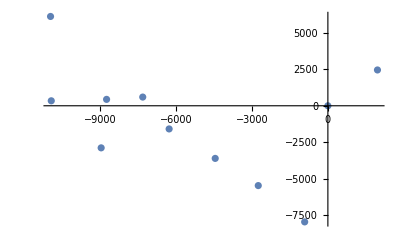

```mathematica
ListPlot[Result]
```

## 3 x3 Example

```mathematica
dm=DistanceMatrix[{{0,0},{2.,1},{0,1}}]
```

{{0.,2.23607,1.},{2.23607,0.,2.},{1.,2.,0.}}

```mathematica
dmM=Table[(dm[[1,j]]^2+dm[[1,i]]^2-dm[[i,j]]^2)/2,{i,1,3},{j,1,3}]
```

{{0.,0.,0.},{0.,5.,1.},{0.,1.,1.}}

```mathematica
{evalsdm,evecsdm}=Eigensystem[dmM]//N
```

{{5.23607,0.763932,0.},{{0.,0.973249,0.229753},{0.,0.229753,-0.973249},{1.,0.,0.}}}

```mathematica
Transpose[evecsdm].DiagonalMatrix[evalsdm].evecsdm
```

{{0.,0.,0.},{0.,5.,1.},{0.,1.,1.}}

```mathematica
Orig=Transpose[evecsdm].√DiagonalMatrix[evalsdm]
```

{{0.,0.,0.},{2.22703,0.200811,0.},{0.525731,-0.850651,0.}}

```mathematica
MatrixForm[Orig]//N
```

(0. | 0. | 0.
2.22703 | 0.200811 | 0.
0.525731 | -0.850651 | 0.)